## Pre

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
nuediff37={#[[1]],#[[2]]/10^(31)}&/@Transpose@N@Import["garching-data/nuediff37array.csv"];
```

```mathematica
nuediff37Red = (DeleteDuplicates@nuediff37)[[;;;;2]];
```

The data is in unit of 10^(31) cm^(-3)

```mathematica
spectFunRaw = Interpolation[nuediff37Red]
```

InterpolatingFunction[{{-1., 1.}}, <>]

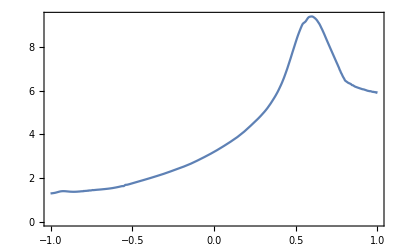

```mathematica
Plot[spectFunRaw[x],{x,-1,1},Frame->True,AxesOrigin->{0,0},Axes->False]
```

```mathematica
spectFun[u_]=CoefficientList[
Fit[nuediff37Red,Table[u^n,{n,0,20}],u],
u].Table[u^n,{n,0,20}]
```

3.1091+3.94885 u+13.6321 u^2+29.7702 u^3-225.442 u^4-633.296 u^5+2004.45 u^6+6141.36 u^7-7352.7 u^8-27716.9 u^9+11634.1 u^10+67595. u^11-3020.74 u^12-95880.5 u^13-16046.9 u^14+79560.6 u^15+24007.7 u^16-35942.6 u^17-14192.4 u^18+6845.04 u^19+3178.78 u^20

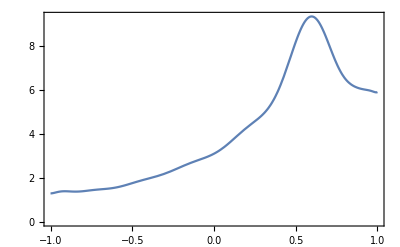

```mathematica
Plot[spectFun[x],{x,-1,1},Frame->True,AxesOrigin->{0,0},Axes->False]
```

```mathematica
SpectrumOmegaNMAA[0.1,1,-1,spectFun]
SpectrumOmegaNMZA[0.1,1,-1,spectFun]
SpectrumOmegaNMZA[0.9,1,-1,spectFun]
SpectrumOmegaNMZA[0.999,1,-1,spectFun]
SpectrumOmegaNMZA[0.9999,1,-1,spectFun]
```

-1.3619

{-1.07968,3.80348}

{-1.87589,6.22454}

{-4.51809,9.84329}

{-5.70431,11.0595}

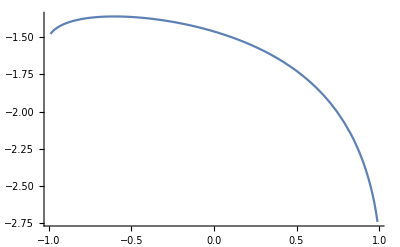

```mathematica
Plot[
SpectrumOmegaNMAA[n,1,-1,spectFun],
{n,-0.99,0.99}
]
```

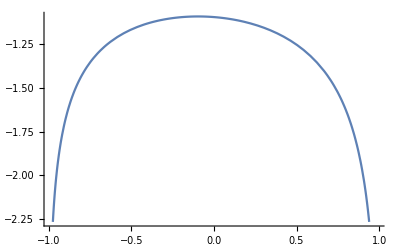

```mathematica
Plot[
SpectrumOmegaNMZA[n,1,-1,spectFun][[1]],
{n,-0.99,0.99}
]
```

```mathematica
pltSpect=ParametricPlot[
{
{n SpectrumOmegaNMAA[n,1,-1,spectFun],SpectrumOmegaNMAA[n,1,-1,spectFun]},
{n *#,#}&/@SpectrumOmegaNMZA[n,1,-1,spectFun]
},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"}
]//Quiet
```

$Aborted

```mathematica
??Export
```

Export[file.ext,expr] exports data to a file, converting it to the format corresponding to the file extension ext. 
Export[file,expr,format] exports data in the specified format.
Export[file,exprs,elems] exports data by treating exprs as elements specified by elems.

Attributes[Export]={Protected,ReadProtected}